## Online Supplementary Material: Mathematica Code for Starving the enemy? Feeding behavior shapes host-parasite interactions Authors: Jessica L. Hite, Alaina C. Pfenning, and Clayton E. Cressler Preliminaries

In the models we are considering here, the host controls its feeding behavior, set by the trait α. The parasite controls its exploitation, controlled by the trait ϵ. For the host, the effects of changing α on population dynamics is context-dependent; we consider four different cases here (and a fifth case detailed separately below). The effects of increasing ϵ, on the other hand, are assumed fixed: increasing ϵ linearly increases virulence (i.e., parasite-induced mortality) but also increases shedding in a saturating way.

We can begin by deriving the invasion fitnesses for a mutant host, and for a mutant parasite. There are a lot of equations here, because we need to consider the dynamics of the resident host infected by the resident parasite (I); the mutant host infected by the resident parasite (Imh); the resident host infected by the mutant parasite (Imp); and the mutant host infected by the mutant parasite (Imhp).

```mathematica
(* host trait = α *)
(* parasite trait = ϵ *)
(* resident susceptible host *)
ds=bs[α] s+bi[α] i+bi[α] imp-β[α] s z-β[α] s zm-μ s+γ[α]i+γ[α] imp;
(* mutant susceptible host *)
dsm=bs[αm] sm+bi[αm] imh+bi[αm] imhp-β[αm] sm z-β[αm] sm zm-μ sm+γ[αm]imh+γ[αm] imhp;
(* resident host infected with resident parasite *)
di=β[α] s z-(μ+v[α,ϵ]+γ[α])i;
(* resident host infected with mutant parasite *)
dimp=β[α] s zm-(μ+v[α,ϵm]+γ[α]) imp;
(* mutant host infected with resident parasite *)
dimh=β[αm] sm z-(μ+v[αm,ϵ]+γ[αm]) imh;
(* mutant host infected with mutant parasite *)
dimhp=β[αm] sm zm-(μ+v[αm,ϵm]+γ[αm]) imhp;
(* resident free-living parasite *)
dz=λ[α,ϵ] i+λ[αm,ϵ] imh-β[α] s z-β[αm] sm z-δ z;
(* mutant free-living parasite *)
dzm=λ[α,ϵm] imp+λ[αm,ϵm] imhp-β[α] s zm-β[αm] sm zm-δ zm;
```

We will use subsets of these equations to compute the invasion fitnesses for the mutant host and the mutant parasite separately. This essentially assumes that we never have invasion of both simultaneously, which also means that Imhp is always 0 during invasion, so it’s dynamics can be ignored.

```mathematica
(* host invasion fitness using the NGT *)
J =D[{ds,di,dz,dsm,dimh},{{s,i,z,sm,imh}}];
MatrixForm[J/.{sm->0,imh->0,zm->0}];
F={{bs[αm],bi[αm]},{0,0}};
V={{β[αm] z+μ,-γ[αm]},{-β[αm] z,μ+v[αm,ϵ]+γ[αm]}};
(J[[4;;5,4;;5]]/.{sm->0,imh->0,zm->0})==F-V;
Inverse[V];
Eigenvalues[-V];
invfitH=Eigenvalues[F.Inverse[V]][[2]]
```

(μ bs[αm]+bs[αm] v[αm,ϵ]+z bi[αm] β[αm]+bs[αm] γ[αm])/(μ^2+μ v[αm,ϵ]+z μ β[αm]+z v[αm,ϵ] β[αm]+μ γ[αm])

```mathematica
(* The invasion fitness is the solution of the recursive equation given below *)
Solve[R==bs[αm]/(β[αm]z+μ)+(β[αm]z)/(β[αm]z+μ)(bi[αm]/(μ+v[αm,ϵ]+γ[αm])+γ[αm]/(μ+v[αm,ϵ]+γ[αm])R),R][[1,1,2]]==invfitH//Simplify
```

True

```mathematica
(* parasite invasion fitness using the NGT *)
J=D[{ds,di,dz,dimp,dzm},{{s,i,z,imp,zm}}];
MatrixForm[J/.{imp->0,zm->0,sm->0}];
F={{0,β[α] s},{λ[α,ϵm],0}};
V={{-(-μ-v[α,ϵm]-γ[α]),0},{0,-(-δ-s β[α])}};
(J/.{imp->0,zm->0,sm->0})[[4;;5,4;;5]]==F-V
Inverse[V];
Eigenvalues[-V];
invfitP=((Eigenvalues[F.Inverse[V]])[[2]])^2
```

True

(s β[α] λ[α,ϵm])/((δ+s β[α]) (μ+v[α,ϵm]+γ[α]))

```mathematica
(* These invasion fitnesses depend on the resident-only equilibrium, which is *)
resEquil=Simplify[Solve[{ds==0,di==0,dz==0}/.{imh->0,imp->0,imhp->0,sm->0,zm->0},{s,i,z}]]
```

{{s→0,i→0,z→0},{s→-(δ (μ+v[α,ϵ]+γ[α]))/(β[α] (μ+v[α,ϵ]+γ[α]-λ[α,ϵ])),i→(δ (μ-bs[α]) (μ+v[α,ϵ]+γ[α]))/((μ-bi[α]+v[α,ϵ]) β[α] (μ+v[α,ϵ]+γ[α]-λ[α,ϵ])),z→-((μ-bs[α]) (μ+v[α,ϵ]+γ[α]))/((μ-bi[α]+v[α,ϵ]) β[α])}}

## Detailed analysis of models of anorexia as host adaptation

```mathematica
(* Context 1: Anorexia functions primarily as Anti-infection Resistance *)
(* {v[αm,ϵ]->v[ϵ],bi[αm]->bs[αm]->bs} *)
(* resident-only equilibrium *)
resEquil/.{v[α,ϵ]->v[ϵ],bi[α]->bs,bs[α]->bs}
```

{{s→0,i→0,z→0},{s→-(δ (μ+v[ϵ]+γ[α]))/(β[α] (μ+v[ϵ]+γ[α]-λ[α,ϵ])),i→(δ (-bs+μ) (μ+v[ϵ]+γ[α]))/((-bs+μ+v[ϵ]) β[α] (μ+v[ϵ]+γ[α]-λ[α,ϵ])),z→-((-bs+μ) (μ+v[ϵ]+γ[α]))/((-bs+μ+v[ϵ]) β[α])}}

```mathematica
(* this gives us signs for a few quantities *)
γ[α]+μ+v[ϵ]-λ[α,ϵ]<0; (* from the s equilibrium *)
μ-bs<0; (* from the i and z equilibria *)
μ-bs+v[ϵ]>0;
```

#### Host evolution only

```mathematica
(* host selection gradient *)
selgradH1=D[invfitH/.{v[αm,ϵ]->v[ϵ],bi[αm]->bs,bs[αm]->bs},αm]/.{αm->α}/.{z->(resEquil[[2,3,2]]/.{v[α,ϵ]->v[ϵ],bi[α]->bs,bs[α]->bs})}//Simplify
(* since bs-μ-v[ϵ] < 0, if β'[α] > 0 and γ'[α] > 0, there is the possibility of a zero of the selection gradient *)
```

((bs-μ) (bs-μ-v[ϵ]) ((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α]))/(bs v[ϵ] β[α] (μ+v[ϵ]+γ[α]))

```mathematica
Solve[selgradH1==0,β'[α]]
```

{{β'[α]→(β[α] γ'[α])/(μ+v[ϵ]+γ[α])}}

```mathematica
(* host ESS condition *)
esscondH1=D[invfitH/.{v[αm,ϵ]->v[ϵ],bi[αm]->bs,bs[αm]->bs},{αm,2}]/.{αm->α}/.{z->(resEquil[[2,3,2]]/.{v[α,ϵ]->v[ϵ],bi[α]->bs,bs[α]->bs})}/.Solve[selgradH1==0,β'[α]][[1]]//Simplify
(* There can be an ESS if (μ+v[ϵ]+γ[α]) β''[α]-β[α] γ''[α] > 0, which would be guaranteed by β''(α)≥0 and γ''(α)<fun0. *)
```

((bs-μ) (bs-μ-v[ϵ]) ((μ+v[ϵ]+γ[α]) β''[α]-β[α] γ''[α]))/(bs v[ϵ] β[α] (μ+v[ϵ]+γ[α]))

```mathematica
params1
```

```mathematica
params1={bmax->2.1,bs->2.1,μ->1.4,γmax->3,v0->0.1,δ->2,βmax->0.1,h->10,he->1,λmax->20}
```

{bmax→2.1,bs→2.1,μ→1.4,γmax→3,v0→0.1,δ→2,βmax→0.1,h→10,he→1,λmax→20}

```mathematica
funcset1={bs[α]->bmax,bi[α]->bmax,β[α]->α/(h+α) βmax,γ[α]->α γmax,λ[ϵ]->(ϵ λmax)/(he+ϵ),λ[α,ϵ]->(ϵ λmax)/(he+ϵ),v[α,ϵ]->v0 ϵ,v[ϵ]->v0 ϵ};
selgradH1/.funcset1/.D[funcset1,α]
```

((h+α) (bs-μ) (bs-v0 ϵ-μ) (-(α βmax γmax)/(h+α)+(-(α βmax)/(h+α)^2+βmax/(h+α)) (α γmax+v0 ϵ+μ)))/(bs v0 α βmax ϵ (α γmax+v0 ϵ+μ))

```mathematica
Solve[(selgradH1/.funcset1/.D[funcset1,α]/.params1/.ϵ->1)==0,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-2.23607},{α→2.23607}}

```mathematica
D[invfitH/.{v[αm,ϵ]->v[ϵ],bi[αm]->bs,bs[αm]->bs},{αm,2}]/.{αm->α}/.{z->(resEquil[[2,3,2]]/.{v[α,ϵ]->v[ϵ],bi[α]->bs,bs[α]->bs})}/.funcset1/.D[funcset1,α]/.{β''[α]->D[α/(h+α),{α,2}],γ''[α]->D[α γmax,{α,2}]}/.params1/.ϵ->1/.{α->2.23606797749979}
```

-1.19479

```mathematica
((μ+v[ϵ]+γ[α]) β''[α]-β[α] γ''[α])/.funcset1/.{β''[α]->D[α/(h+α),{α,2}],γ''[α]->D[α γmax,{α,2}]}/.params1/.ϵ->1/.{α->2.23606797749979}
```

-0.0896092

```mathematica
((bs-μ) (bs-μ-v[ϵ]))/(bs v[ϵ] β[α] (μ+v[ϵ]+γ[α]))/.funcset1/.{β''[α]->D[α/(h+α),{α,2}],γ''[α]->D[α γmax,{α,2}]}/.params1/.ϵ->1/.{α->2.23606797749979}
```

13.3333

```mathematica
resEquil/.{v[α,ϵ]->v[ϵ],bi[α]->bs,bs[α]->bs} /.funcset1/.params1/.ϵ->1/.{α->2.23606797749979}
```

{{s→0,i→0,z→0},{s→501.356,i→-584.916,z→-524.025}}

#### Pathogen evolution only

Now we need to consider the pathogen evolution case. As is typical, as long as λ is a saturating function of ϵ, there will be a singular strategy and it will be an ESS.

```mathematica
selgradP1=Simplify[D[invfitP/.{v[α,ϵm]->v[ϵm],λ[α,ϵm]->λ[ϵm]},ϵm]]/.ϵm->ϵ
esscondP1=Simplify[D[invfitP/.{v[α,ϵm]->v[ϵm],λ[α,ϵm]->λ[ϵm]},{ϵm,2}]]/.ϵm->ϵ/.Solve[selgradP1==0,λ'[ϵ]][[1]]//Simplify
```

(s β[α] (-λ[ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) λ'[ϵ]))/((δ+s β[α]) (μ+v[ϵ]+γ[α])^2)

(s β[α] (-λ[ϵ] v''[ϵ]+(μ+v[ϵ]+γ[α]) λ''[ϵ]))/((δ+s β[α]) (μ+v[ϵ]+γ[α])^2)

#### Coevolution

Here we are looking for simultaneous vanishing of both selection gradients.

```mathematica
Solve[fitgradH1==0,α]
```

{{α→(-h v0 ϵ-h μ-√(-h^2 v0 γmax ϵ-h^2 γmax μ))/(γmax+v0 ϵ+μ)},{α→(-h v0 ϵ-h μ+√(-h^2 v0 γmax ϵ-h^2 γmax μ))/(γmax+v0 ϵ+μ)}}

```mathematica
-h v0 ϵ-h μ+√(-h^2 v0 γmax ϵ-h^2 γmax μ)>0;
√(-h^2 v0 γmax ϵ-h^2 γmax μ)>h v0 ϵ+h μ
Simplify[Expand[-h^2 v0 γmax ϵ-h^2 γmax μ>(h v0 ϵ+h μ)^2]]
```

√(-h^2 v0 γmax ϵ-h^2 γmax μ)>h v0 ϵ+h μ

h^2 (v0 ϵ+μ) (γmax+v0 ϵ+μ)<0

```mathematica
fitgradP1
```

-(v0 ϵ λmax)/(hp+ϵ)+(-(ϵ λmax)/(hp+ϵ)^2+λmax/(hp+ϵ)) ((α γmax)/(h+α)+v0 ϵ+μ)

```mathematica
params1={bmax->2,μ->1.5,v0->0.1,δ->0.1,λ->1,βmax->0.1,h->3,hp->1,γmax->1.5,λmax->10};fitgradH1=((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α])/.{β[α]->βmax α^2,γ[α]->γmax α/(h+α),β'[α]->βmax,γ'[α]->D[γmax α/(h+α),α]}/.{v[ϵ]->v0 ϵ};
fitgradP1=(-λ[ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) λ'[ϵ])/.{λ[ϵ]->λmax ϵ/(hp+ϵ),v[ϵ]->v0 ϵ,γ[α]->γmax α/(h+α),λ'[ϵ]->D[λmax ϵ/(hp+ϵ),ϵ],v'[ϵ]->D[v0 ϵ,ϵ]};
coESS=FindRoot[{fitgradH1/.params1,fitgradP1/.params1},{{α,1},{ϵ,10}}]
```

{α→18.1803,ϵ→5.27971}

### Context 2: Anorexia functions primarily as Anti-growth resistance.

In this context, the host uses anorexia to either (or both) reduce shedding rate (λ) or increase recovery rate (γ). Note these effects could also be caused if anorexia functions to avoid ingesting unpalatable or immunosuppressive resources.

```mathematica
(* {v[αm,ϵ]->v[ϵ],γ[αm]->γ,bi[αm]->bs[αm]} *)
(* resident-only equilibrium *)
resEquil/.{v[α,ϵ]->v[ϵ],β[α]->β,bs[α]->bs}
```

{{s→0,i→0,z→0},{s→-(δ (μ+v[ϵ]+γ[α]))/(β (μ+v[ϵ]+γ[α]-λ[α,ϵ])),i→(δ (-bs+μ) (μ+v[ϵ]+γ[α]))/(β (μ-bi[α]+v[ϵ]) (μ+v[ϵ]+γ[α]-λ[α,ϵ])),z→-((-bs+μ) (μ+v[ϵ]+γ[α]))/(β (μ-bi[α]+v[ϵ]))}}

```mathematica
(* this gives us signs for a few quantities *)
γ[α]+μ+v[ϵ]-λ[α,ϵ]<0; (* from the s equilibrium *)
μ-bs[α]<0; (* from the i and z equilibria *)
μ-bi[α]+v[ϵ]>0;
```

#### Host evolution

The selection gradient is:

```mathematica
selgradH2=D[invfitH/.{v[αm,ϵ]->v[ϵ],β[αm]->β,bs[αm]->bs},αm]/.{αm->α}/.{resEquil[[2,3]]/.{v[α,ϵ]->v[ϵ],β[α]->β,bs[α]->bs}}//Simplify
```

((bs-μ) ((μ+v[ϵ]+γ[α]) bi'[α]+(μ-bi[α]+v[ϵ]) γ'[α]))/((-μ bi[α]+bs (μ+v[ϵ])) (μ+v[ϵ]+γ[α]))

The sign of the selection gradient will be given by (all other terms are positive):

```mathematica
((μ+v[ϵ]+γ[α]) bi'[α]+(μ-bi[α]+v[ϵ]) γ'[α])
```

From this expression it is clear that b_i'(α) and γ'(α) must have opposite signs for a singular strategy to exist. For such a singular strategy to be an ESS requires that the following expression is negative. This will be guaranteed if b_i''(α)≤0 and γ''(α)≤ 0 (as long as both are not zero). It is also possible if they have opposite signs. But it is not possible if both second derivatives are positive.

```mathematica
esscondH2=D[invfitH/.{v[αm,ϵ]->v[ϵ],β[αm]->β,bs[αm]->bs},{αm,2}]/.{αm->α}/.{resEquil[[2,3]]/.{v[α,ϵ]->v[ϵ],β[α]->β,bs[α]->bs}}/.Solve[((μ+v[ϵ]+γ[α]) bi'[α]+(μ-bi[α]+v[ϵ]) γ'[α])==0,γ'[α]][[1]]//Simplify
```

((bs-μ) ((μ+v[ϵ]+γ[α]) bi''[α]+(μ-bi[α]+v[ϵ]) γ''[α]))/((-μ bi[α]+bs (μ+v[ϵ])) (μ+v[ϵ]+γ[α]))

For example, with b_i(α)=b_s α/(h+α) and γ(α)=γ_max/α, it is possible that there will be a singular strategy, though not guaranteed.

```mathematica
Expand[Numerator[Simplify[esscondH2/.{bi[α]->bs α/(h+α),γ[α]->γmax/α,bi''[α]->D[bs α/(h+α),{α,2}],γ''[α]->D[γmax/α,{α,2}]}]][[2]]]
```

-(2 bs h γmax)/(α (h+α)^3)-(2 bs γmax)/(α^2 (h+α))-(2 bs h μ)/(h+α)^3+(2 γmax μ)/α^3-(2 bs h v[ϵ])/(h+α)^3+(2 γmax v[ϵ])/α^3

Try out with some parameters, remembering the equalities that must be satisfied:

```mathematica
γ[α]+μ+v[ϵ]-λ[α,ϵ]<0; (* from the s equilibrium *)
μ-bs<0; (* from the i and z equilibria *)
μ-bi[α]+v[ϵ]>0;
```

Also, though we haven’t gotten to this yet, we can assume a linear relationship between virulence and exploitation, v(ϵ)=v_min ϵ.

```mathematica
params={bs->0.2,μ->0.1,v0->0.2,ϵ->1,γmax->0.2,h->0.4,he->1,β->0.1,δ->1};
```

```mathematica
singst=Solve[Simplify[((μ+v[ϵ]+γ[α]) bi'[α]+(μ-bi[α]+v[ϵ]) γ'[α])/.{bi[α]->bs α/(h+α),γ[α]->γmax/α,bi'[α]->D[bs α/(h+α),α],γ'[α]->D[γmax/α,α]}]==0,α][[2]]/.v[ϵ]->v0 ϵ/.params
```

{α→4.52982}

Does this produce a positive equilibrium? Again, we’ll have to specify how λ is affected by anorexia and exploitation: let’s just assume that λ(α,ϵ)=αϵ/(h_e+ϵ) for simplicity (and because I know that this saturating response to exploitation is needed for an ESS exploitation to exist). It does, indeed.

```mathematica
resEquil/.{v[α,ϵ]->v[ϵ],β[α]->β,bs[α]->bs}/.{bi[α]->bs α/(h+α),γ[α]->γmax/α}/.{v[ϵ]->v0 ϵ,λ[α,ϵ]->α ϵ/(he+ϵ)}/.params/.singst
```

{{s→0,i→0,z→0},{s→1.79175,i→1.54158,z→2.96101}}

Is this singular strategy evolutionarily stable? It is not, at least at the current parameters. Some random exploration of parameter space failed to find any location where there was an ESS.

```mathematica
essEval=esscondH2/.{bi[α]->bs α/(h+α),γ[α]->γmax/α,bi''[α]->D[bs α/(h+α),{α,2}],γ''[α]->D[γmax/α,{α,2}]}/.{v[ϵ]->v0 ϵ}/.singst/.params
```

0.000283318

Here is an adjustment that produces an ESS. This γ(α) function has a positive second derivative, but is almost linear, which is nice because it prevents needing to worry about γ(α) becoming negative. It is also robust to a lot of variation in ϵ, which is good for the coevolution case.

```mathematica
params={bs->0.2,μ->0.1,v0->0.2,ϵ->1,γmax->0.2,h->0.2,he->1,β->0.1,a->0.1,δ->1};
singst=FindRoot[(Simplify[((μ+v[ϵ]+γ[α]) bi'[α]+(μ-bi[α]+v[ϵ]) γ'[α])/.{bi[α]->bs α/(h+α),γ[α]->γmax/α^a,bi'[α]->D[bs α/(h+α),α],γ'[α]->D[γmax/α^a,α]}]/.{v[ϵ]->v0 ϵ,λ[α,ϵ]->α ϵ/(he+ϵ)}/.params),{α,1}]
resEquil/.{v[α,ϵ]->v[ϵ],β[α]->β,bs[α]->bs}/.{bi[α]->bs α/(h+α),γ[α]->γmax/α^a}/.{v[ϵ]->v0 ϵ,λ[α,ϵ]->α ϵ/(he+ϵ)}/.params/.singst
esscondH2/.{bi[α]->bs α/(h+α),γ[α]->γmax/α^a,bi''[α]->D[bs α/(h+α),{α,2}],γ''[α]->D[γmax/α^a,{α,2}]}/.{v[ϵ]->v0 ϵ}/.params/.singst
```

{α→10.8009}

{{s→0,i→0,z→0},{s→0.925888,i→0.893403,z→4.4159}}

-0.0000654773

#### Parasite evolution

There will likely be a singular strategy if v’(ϵ) and ∂λ/∂ϵ have the same sign (both positive):

```mathematica
Simplify[D[invfitP/.{β[α]->α,v[α,ϵm]->v[ϵm]},ϵm]]/.ϵm->ϵ
```

(s α (-λ[α,ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) λ^(0,1)[α,ϵ]))/((s α+δ) (μ+v[ϵ]+γ[α])^2)

Any such singular strategy will be an ESS if λ''(ϵ)≥0 and ∂λ/∂ϵ≤0.

```mathematica
Simplify[D[invfitP/.{β[α]->α,v[α,ϵm]->v[ϵm]},{ϵm,2}]/.{ϵm->ϵ}/.Solve[(D[invfitP/.{β[α]->α,v[α,ϵm]->v[ϵm]},ϵm]/.ϵm->ϵ)==0,v'[ϵ]]]
```

{(s α (-λ[α,ϵ] v''[ϵ]+(μ+v[ϵ]+γ[α]) λ^(0,2)[α,ϵ]))/((s α+δ) (μ+v[ϵ]+γ[α])^2)}

Using the parameters and functional forms above, you can see that the singular strategy depends on anorexia (as the singular anorexia depended on exploitation). However, this only comes through the dependence of shedding on anorexia.

```mathematica
singst=Solve[((-λ[α,ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) Derivative[0,1][λ][α,ϵ])/.{β[α]->α,v[ϵ]->v0 ϵ,λ[α,ϵ]->α ϵ/(he+ϵ),γ[α]->γmax/α^a,v'[ϵ]->v0,Derivative[0,1][λ][α,ϵ]->D[α ϵ/(he+ϵ),ϵ]})==0,ϵ]
```

{{ϵ→-(√(he α^-a γmax+he μ))/(√v0)},{ϵ→(√(he α^-a γmax+he μ))/(√v0)}}

```mathematica
Solve[((-λ[α,ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) Derivative[0,1][λ][α,ϵ])/.{ϵ->ϵESS[α]})==0,v'[ϵESS[α]]]
```

{{v'[ϵESS[α]]→((μ+v[ϵESS[α]]+γ[α]) λ^(0,1)[α,ϵESS[α]])/λ[α,ϵESS[α]]}}

How will changing α affect the evolution of exploitation?

```mathematica
Simplify[Solve[(D[(-λ[α,ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) Derivative[0,1][λ][α,ϵ])/.{ϵ->ϵESS[α]},α])==0,ϵESS'[α]]]/.{ϵESS[α]->ϵ̂}
```

{{ϵESS'[α]→(γ'[α] λ^(0,1)[α,ϵ̂]-v'[ϵ̂] λ^(1,0)[α,ϵ̂]+(μ+v[ϵ̂]+γ[α]) λ^(1,1)[α,ϵ̂])/(λ[α,ϵ̂] v''[ϵ̂]-(μ+v[ϵ̂]+γ[α]) λ^(0,2)[α,ϵ̂])}}

The denominator is the opposite of the ESS condition, so we know that it must be positive. Thus the sign depends entirely on the numerator.
γ'[α] λ^(0,1)[α,ϵ̂] is either (negative)*(positive) = negative (if anorexia increases recovery) or 0 (if anorexia only affects shedding)
-v'[ϵ̂] λ^(1,0)[α,ϵ̂]is -(positive)*(positive) = negative (if anorexia decreases shedding) or 0 (if anorexia only affects recovery)
(μ+v[ϵ̂]+γ[α]) λ^(1,1)[α,ϵ̂] is likely positive or zero (if there is no interaction between anorexia and exploitation)
So regardless of whether anorexia affects shedding, recovery, or both, increasing feeding will drive the evolution of reduced exploitation.

```mathematica
Table[singst[[2]]/.params,{α,1,20}]
```

{{ϵ→1.22474},{ϵ→1.19709},{ϵ→1.18151},{ϵ→1.17071},{ϵ→1.16247},{ϵ→1.15584},{ϵ→1.15029},{ϵ→1.14554},{ϵ→1.14138},{ϵ→1.13769},{ϵ→1.13437},{ϵ→1.13136},{ϵ→1.12861},{ϵ→1.12608},{ϵ→1.12373},{ϵ→1.12154},{ϵ→1.1195},{ϵ→1.11758},{ϵ→1.11577},{ϵ→1.11406}}

#### Coevolution

This will have to be done numerically.

Using the functions and parameters above,

```mathematica
params={bs->0.2,μ->0.1,v0->0.2,γmax->0.2,h->0.2,he->1,β->0.1,a->0.1,δ->1};fitgradH=Simplify[((μ+v[ϵ]+γ[α]) bi'[α]+(μ-bi[α]+v[ϵ]) γ'[α])/.{bi[α]->bs α/(h+α),γ[α]->γmax/α^a,bi'[α]->D[bs α/(h+α),α],γ'[α]->D[γmax/α^a,α]}]/.{v[ϵ]->v0 ϵ,λ[α,ϵ]->α ϵ/(he+ϵ)};
fitgradP=(-λ[α,ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) Derivative[0,1][λ][α,ϵ])/.{γ[α]->γmax/α^a,λ[α,ϵ]->α ϵ/(he+ϵ),v[ϵ]->v0 ϵ,Derivative[0,1][λ][α,ϵ]->D[α ϵ/(he+ϵ),ϵ],v'[ϵ]->v0};
FindRoot[{fitgradH/.params,fitgradP/.params},{{α,1},{ϵ,1}}]
```

{α→8.74156,ϵ→1.1424}

Just for giggles, here’s how those change with changing some other ecological factor, in this case host lifespan. As host lifespan decreases (background mortality increases), the anorexic response increases, leading to the coevolution of more virulent pathogens.

```mathematica
params0={bs->0.4,v0->0.3,γmax->0.2,h->0.2,he->1,β->0.1,a->0.1,δ->1};
Table[FindRoot[{fitgradH/.params,fitgradP/.params},{{α,1},{ϵ,1}}],{μ,0.08,0.39,0.01}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{α→9.0422,ϵ→1.1412},{α→9.62408,ϵ→1.13902},{α→8.74156,ϵ→1.1424},{α→8.0013,ϵ→1.14553},{α→7.37127,ϵ→1.14845},{α→6.82841,ϵ→1.15118},{α→6.35571,ϵ→1.15376},{α→5.94033,ϵ→1.1562},{α→5.57241,ϵ→1.15852},{α→5.24421,ϵ→1.16073},{α→4.9496,ϵ→1.16284},{α→4.68367,ϵ→1.16487},{α→4.44241,ϵ→1.16682},{α→4.22252,ϵ→1.1687},{α→4.02128,ϵ→1.17051},{α→3.8364,ϵ→1.17226},{α→3.66596,ϵ→1.17396},{α→3.50832,ϵ→1.1756},{α→3.36209,ϵ→1.1772},{α→3.22606,ϵ→1.17876},{α→3.09921,ϵ→1.18027},{α→2.98062,ϵ→1.18175},{α→2.86951,ϵ→1.1832},{α→2.7652,ϵ→1.18461},{α→2.66707,ϵ→1.18598},{α→2.57458,ϵ→1.18734},{α→2.48726,ϵ→1.18866},{α→2.40469,ϵ→1.18996},{α→2.32647,ϵ→1.19123},{α→2.25228,ϵ→1.19248},{α→2.18181,ϵ→1.19371},{α→2.11477,ϵ→1.19492}}

Here it is if you allow a more interesting interaction between α and ϵ (which could actually exist if, for example, α and ϵ both have linear effects on parasite burden, and that has a nonlinear effect on shedding (e.g., a saturating effect), then things may be more interesting. Turns out they are just hard to analyze!

```mathematica
params={bs->0.3,μ->0.1,v0->0.2,γmax->0.2,h->0.5,he->1,β->0.1,a->0.1,δ->1};
fitgradH=Simplify[((μ+v[ϵ]+γ[α]) bi'[α]+(μ-bi[α]+v[ϵ]) γ'[α])/.{bi[α]->bs α/(h+α),γ[α]->γmax/α^a,bi'[α]->D[bs α/(h+α),α],γ'[α]->D[γmax/α^a,α]}]/.{v[ϵ]->v0 ϵ,λ[α,ϵ]->(α ϵ)/(he+α ϵ)};
fitgradP=(-λ[α,ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) Derivative[0,1][λ][α,ϵ])/.{γ[α]->γmax/α^a,λ[α,ϵ]->(α ϵ)/(he+α ϵ),v[ϵ]->v0 ϵ,Derivative[0,1][λ][α,ϵ]->D[(α ϵ)/(he+α ϵ),ϵ],v'[ϵ]->v0};
coESS=FindRoot[{fitgradH/.params,fitgradP/.params},{{α,4},{ϵ,1}}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{α→24.6032,ϵ→0.223099}

### Context 4: Anorexia functions primarily as Tolerance.

Here, the host uses anorexia to reduce virulence, at the cost of reduced birth rate.

```mathematica
(* {v[αm,ϵ]->v[ϵ],γ[αm]->γ,bi[αm]->bs[αm]} *)
(* resident-only equilibrium *)
resEquil/.{γ[α]->γ,β[α]->β,bs[α]->bs,λ[α,ϵ]->λ[ϵ]}
```

{{s→0,i→0,z→0},{s→-(δ (γ+μ+v[α,ϵ]))/(β (γ+μ+v[α,ϵ]-λ[ϵ])),i→(δ (-bs+μ) (γ+μ+v[α,ϵ]))/(β (μ-bi[α]+v[α,ϵ]) (γ+μ+v[α,ϵ]-λ[ϵ])),z→-((-bs+μ) (γ+μ+v[α,ϵ]))/(β (μ-bi[α]+v[α,ϵ]))}}

```mathematica
(* this gives us signs for a few quantities *)
γ+μ+v[α,ϵ]-λ[ϵ]<0; (* from the s equilibrium *)
μ-bs<0; (* from the i and z equilibria *)
μ-bi[α]+v[α,ϵ]>0;
```

#### Host evolution

The selection gradient is the following:

```mathematica
(* selection gradient *)
selgradH3=D[invfitH/.{γ[αm]->γ,β[αm]->β,bs[αm]->bs},αm]/.{αm->α}/.(resEquil[[2,3]]/.{γ[α]->γ,β[α]->β,bs[α]->bs,λ[α,ϵ]->λ[ϵ]})//Simplify
```

((bs-μ) ((γ+μ+v[α,ϵ]) bi'[α]-(γ+bi[α]) v^(1,0)[α,ϵ]))/((γ+μ+v[α,ϵ]) (-μ bi[α]+bs (μ+v[α,ϵ])))

The selection gradient will only possibly admit a zero if b_i'(α) and ∂v/∂α have the same sign.

```mathematica
(* ESS condition *)
esscondH3=D[invfitH/.{γ[αm]->γ,β[αm]->β,bs[αm]->bs},{αm,2}]/.{αm->α}/.(resEquil[[2,3]]/.{γ[α]->γ,β[α]->β,bs[α]->bs,λ[α,ϵ]->λ[ϵ]})/.Solve[selgradH3==0,Derivative[1,0][v][α,ϵ]][[1]]//FullSimplify
(* It will be an ESS if bi''[α] < 0 and v''[α] > 0 *)
(* It will NOT be an ESS if bi''[α] > 0 and v''[α] < 0 *)
(* Otherwise it is possible for it to be an ESS *)
```

((bs-μ) ((γ+μ+v[α,ϵ]) bi''[α]-(γ+bi[α]) v^(2,0)[α,ϵ]))/((γ+μ+v[α,ϵ]) (-μ bi[α]+bs (μ+v[α,ϵ])))

A singular strategy will be an ESS if b_i''(α)≤0 and ∂^2 v/∂α^2≥0. If one of this conditions is not met, it is still possible for there to be a singular strategy, but not if neither are met. For example, one possibility would be that birth rate is a saturating function of anorexia whereas virulence is a linear function of anorexia.

```mathematica
singpts=Solve[(selgradH3/.{v[α,ϵ]->v0 α ϵ, bi[α]->bs α/(h+α),Derivative[1,0][v][α,ϵ]->v0 ϵ, bi'[α]->D[bs α/(h+α),α]})==0,α]//Simplify
```

{{α→(-bs h v0 γ ϵ+h v0 γ ϵ μ+√(bs h v0 ϵ (bs-μ)^2 (bs (γ+μ)+γ (γ-h v0 ϵ+μ))))/(v0 (bs+γ) ϵ (bs-μ))},{α→-(bs h v0 γ ϵ-h v0 γ ϵ μ+√(bs h v0 ϵ (bs-μ)^2 (bs (γ+μ)+γ (γ-h v0 ϵ+μ))))/(v0 (bs+γ) ϵ (bs-μ))}}

As you increase the exploitation rate, the ES host strategy is increased anorexia, as you would expect.

```mathematica
Table[singpts[[1,1,2]]/.{bs->0.3,μ->0.1,v0->0.2,γ->0.2,h->0.5,he->1,β->0.1,a->0.1,δ->1},{ϵ,0.5,2.5,0.1}]
```

{0.716515,0.630662,0.563451,0.508872,0.463325,0.4245,0.390839,0.361249,0.334933,0.311301,0.289898,0.270372,0.252444,0.23589,0.220526,0.206202,0.192792,0.180191,0.16831,0.157071,0.14641}

#### Parasite evolution

The selection gradient is:

```mathematica
selgradP3=D[invfitP/.{γ[α]->γ,β[α]->β,bs[α]->bs,λ[α,ϵm]->λ[ϵm]},ϵm]//Simplify
```

(s β ((γ+μ+v[α,ϵm]) λ'[ϵm]-λ[ϵm] v^(0,1)[α,ϵm]))/((s β+δ) (γ+μ+v[α,ϵm])^2)

Any singular strategy will be stable if this condition is met (e.g., if λ is a saturating function of exploitation, whereas virulence is a linear function of it):

```mathematica
D[selgradP3,ϵm]/.Solve[selgradP3==0,λ'[ϵm]][[1]]//Simplify
```

(s β ((γ+μ+v[α,ϵm]) λ''[ϵm]-λ[ϵm] v^(0,2)[α,ϵm]))/((s β+δ) (γ+μ+v[α,ϵm])^2)

```mathematica
(Numerator[selgradP3][[3]]/.{ϵm->ϵ}/.{v[α,ϵ]->v0 α ϵ, λ[ϵ]->(λ0 ϵ)/(he+ϵ),Derivative[0,1][v][α,ϵ]->v0 α,λ'[ϵ]->D[(λ0 ϵ)/(he+ϵ),ϵ]})
```

-(v0 α ϵ λ0)/(he+ϵ)+(-(ϵ λ0)/(he+ϵ)^2+λ0/(he+ϵ)) (γ+v0 α ϵ+μ)

Here is the singular strategy for likely functions. Note that anorexia shows up in the denominator of this expression, implying that the more the host eats, the lower the virulence will be.

```mathematica
singpts=Solve[(Numerator[selgradP3][[3]]/.{ϵm->ϵ}/.{v[α,ϵ]->v0 α ϵ, λ[ϵ]->(λ0 ϵ)/(he+ϵ),Derivative[0,1][v][α,ϵ]->v0 α,  λ'[ϵ]->D[(λ0 ϵ)/(he+ϵ),ϵ]})==0,ϵ]
```

{{ϵ→-(√he √(γ+μ))/(√v0 √α)},{ϵ→(√he √(γ+μ))/(√v0 √α)}}

```mathematica
singpts/.{bs->0.3,μ->0.1,v0->0.2,γ->0.2,h->0.5,he->1,β->0.1,a->0.1,δ->1}/.α->1
```

{{ϵ→-1.22474},{ϵ→1.22474}}

#### Coevolution

It turns out to be rather difficult to find an appropriate and workable set of parameters. Most of the time, you end up in a spot where there is not a feasible coESS.

```mathematica
params={bs->0.3,μ->0.2,v0->0.5,γ->0.2,h->1,he->1,β->0.1,a->0.1,δ->1,λ0->1};
fitgradH=((γ+μ+v[α,ϵ]) bi'[α]-(γ+bi[α]) Derivative[1,0][v][α,ϵ])/.{v[α,ϵ]->v0 α ϵ, bi[α]->bs α/(h+α),Derivative[1,0][v][α,ϵ]->v0 ϵ, bi'[α]->D[bs α/(h+α),α]}
fitgradP=((γ+μ+v[α,ϵ]) λ'[ϵ]-λ[ϵ] Derivative[0,1][v][α,ϵ])/.{v[α,ϵ]->v0 α ϵ, λ[ϵ]->(λ0 ϵ)/(he+ϵ),Derivative[0,1][v][α,ϵ]->v0 α,  λ'[ϵ]->D[(λ0 ϵ)/(he+ϵ),ϵ]}
coESS=FindRoot[{fitgradH/.params,fitgradP/.params},{{ϵ,1},{α,1}},AccuracyGoal->15]
```

-v0 ((bs α)/(h+α)+γ) ϵ+(-(bs α)/(h+α)^2+bs/(h+α)) (γ+v0 α ϵ+μ)

-(v0 α ϵ λ0)/(he+ϵ)+(-(ϵ λ0)/(he+ϵ)^2+λ0/(he+ϵ)) (γ+v0 α ϵ+μ)

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{ϵ→1.28574,α→0.16123}

Looking at the host ESS, what is required for a positive real ESS?

```mathematica
hostESS=Assuming[bs>μ,FullSimplify[(-bs h v0 γ ϵ+h v0 γ ϵ μ+√(bs h v0 ϵ (bs-μ)^2 (bs (γ+μ)+γ (γ-h v0 ϵ+μ))))/(v0 (bs+γ) ϵ (bs-μ))]]
```

(-h v0 γ ϵ+√(bs h v0 ϵ (bs (γ+μ)+γ (γ-h v0 ϵ+μ))))/(v0 (bs+γ) ϵ)

```mathematica
-h v0 γ ϵ+√(bs h v0 ϵ (bs (γ+μ)+γ (γ-h v0 ϵ+μ)))>0;
√(bs h v0 ϵ (bs (γ+μ)+γ (γ-h v0 ϵ+μ)))>h v0 γ ϵ;
(√(bs h v0 ϵ (bs (γ+μ)+γ (γ-h v0 ϵ+μ))))^2>(h v0 γ ϵ)^2;
Simplify[Expand[(√(bs h v0 ϵ (bs (γ+μ)+γ (γ-h v0 ϵ+μ))))^2>(h v0 γ ϵ)^2]]
```

h v0 (bs+γ) ϵ (h v0 γ ϵ-bs (γ+μ))<0

Based on this, it seems that if we make b_s, γ, and μ larger, we should be able to get a coESS. And that is true. So, above, we may want to try to increase the parameter values so we can be using the same default set of parameter values across all cases.

```mathematica
params={bs->3,μ->2,v0->0.5,γ->2,h->1,he->1,β->0.1,a->0.1,δ->1,λ0->1};
fitgradH=((γ+μ+v[α,ϵ]) bi'[α]-(γ+bi[α]) Derivative[1,0][v][α,ϵ])/.{v[α,ϵ]->v0 α ϵ, bi[α]->bs α/(h+α),Derivative[1,0][v][α,ϵ]->v0 ϵ, bi'[α]->D[bs α/(h+α),α]};
fitgradP=((γ+μ+v[α,ϵ]) λ'[ϵ]-λ[ϵ] Derivative[0,1][v][α,ϵ])/.{v[α,ϵ]->v0 α ϵ, λ[ϵ]->(λ0 ϵ)/(he+ϵ),Derivative[0,1][v][α,ϵ]->v0 α,  λ'[ϵ]->D[(λ0 ϵ)/(he+ϵ),ϵ]};
coESS=FindRoot[{fitgradH/.params,fitgradP/.params},{{ϵ,1},{α,1}},AccuracyGoal->15]
fitgradH/.params/.coESS
fitgradP/.params/.coESS
D[fitgradH,α]/.params/.coESS
D[fitgradP,ϵ]/.params/.coESS
```

{ϵ→3.44574,α→0.673789}

8.88178×10^-16

-2.22045×10^-16

-6.60345

-0.117468

### Context 3: Anti-growth Resistance but with immunopathology.

In this context, the host uses anorexia to either (or both) reduce shedding rate (λ) or increase recovery rate (γ). Note these effects could also be caused if anorexia functions to avoid ingesting unpalatable or immunosuppressive resources.

```mathematica
(* resident-only equilibrium *)
resEquil/.{β[α]->βmax,bs[α]->bmax,bi[α]->bmax,λ[α,ϵ]->λ[ϵ]} 

(* this gives us signs for a few quantities *)
γ[α]+μ+v[α,ϵ]-λ[ϵ]<0; (* from the s equilibrium *)
μ-bmax<0; (* from the i and z equilibria *)
μ-bmax+v[α,ϵ]>0;
```

{{s→0,i→0,z→0},{s→-(δ (μ+v[α,ϵ]+γ[α]))/(βmax (μ+v[α,ϵ]+γ[α]-λ[ϵ])),i→(δ (-bmax+μ) (μ+v[α,ϵ]+γ[α]))/(βmax (-bmax+μ+v[α,ϵ]) (μ+v[α,ϵ]+γ[α]-λ[ϵ])),z→-((-bmax+μ) (μ+v[α,ϵ]+γ[α]))/(βmax (-bmax+μ+v[α,ϵ]))}}

#### Host evolution

```mathematica
(* selection gradient *)
selgradH4=D[invfitH/.{β[αm]->βmax,bs[αm]->bmax,bi[αm]->bmax},αm]/.{αm->α}/.(resEquil[[2,3]]/.{β[α]->βmax,bs[α]->bmax,bi[α]->bmax,λ[α,ϵ]->λ[ϵ]})//Simplify
(* for there to be an ESS, γ'(α) and ∂v/∂α both have to have the same sign - the biological interpretation of anorexia as "pyrrhic victory" implies that both must be NEGATIVE *)
```

-((bmax-μ) ((bmax-μ-v[α,ϵ]) γ'[α]+(bmax+γ[α]) v^(1,0)[α,ϵ]))/(bmax v[α,ϵ] (μ+v[α,ϵ]+γ[α]))

```mathematica
(* ESS condition *)
esscondH4=FullSimplify[D[invfitH/.{β[αm]->βmax,bs[αm]->bmax,bi[αm]->bmax},{αm,2}]/.{αm->α}/.(resEquil[[2,3]]/.{β[α]->βmax,bs[α]->bmax,bi[α]->bmax,λ[α,ϵ]->λ[ϵ]})/.Solve[selgradH4==0,γ'[α]][[1]]]
(* Any singular strategy WILL BE an ESS if v''(α) > 0 and γ''(α) < 0 *)
(* It WILL NOT be an ESS if v''(α) < 0 and γ''(α) > 0 *)
(* Otherwise it may be an ESS *)
```

((bmax-μ) ((-bmax+μ+v[α,ϵ]) γ''[α]-(bmax+γ[α]) v^(2,0)[α,ϵ]))/(bmax v[α,ϵ] (μ+v[α,ϵ]+γ[α]))

In this case, anorexia as anti-growth resistance but with immunopathology turns out to require very particular functional forms to be able to find a feasible ESS at a feasible equilibrium. In particular, we need to satisfy all of these conditions simultaneously:

```mathematica
funcset4={bs[α]->bmax,bi[α]->bmax,β[α]->βmax,λ[α,ϵ]->λmax ϵ/(he+ϵ),γ[α]->γmax/α^a,v[α,ϵ]->v0 ϵ (1-e α),γ'[α]->D[γmax/α^a,α],Derivative[1,0][v][α,ϵ]->D[v0 ϵ (1-e α),α],λ[ϵ]->λmax ϵ/(he+ϵ),λ'[ϵ]->D[λmax ϵ/(he+ϵ),ϵ],Derivative[0,1][v][α,ϵ]->D[v0 ϵ (1-e α),ϵ]};
Expand[Numerator[Simplify[((-bmax+μ+v[α,ϵ]) γ'[α]-(bmax+γ[α]) Derivative[1,0][v][α,ϵ])/.funcset4]]]==0
Denominator[(resEquil[[2]]/.funcset4)[[1,2]]][[2]]<0
(-Numerator[(resEquil[[2]]/.funcset4)[[2,2]]][[2]])>0
(-Denominator[(resEquil[[2]]/.funcset4)[[2,2]]][[2]])<0
```

a bmax γmax+bmax e v0 α^(1+a) ϵ-a v0 γmax ϵ+e v0 α γmax ϵ+a e v0 α γmax ϵ-a γmax μ==0

α^-a γmax+v0 (1-e α) ϵ-(ϵ λmax)/(he+ϵ)+μ<0

bmax-μ>0

bmax-v0 (1-e α) ϵ-μ<0

A linear function for virulence may make this challenging. For example, at its maximum (α = 1/e) where virulence is 0, it is impossible to have a feasible equilibrium.

```mathematica
Simplify[((-bmax+μ+v[α,ϵ]) γ'[α]-(bmax+γ[α]) Derivative[1,0][v][α,ϵ])/.funcset4]
```

α^(-1-a) (e v0 α (bmax α^a+γmax) ϵ+a γmax (bmax+v0 (-1+e α) ϵ-μ))

Looking at the selection gradient, it is clear that it is positive near both ends (α = 0 and α = 1/e) unless ϵ is large

```mathematica
params={bmax->3,μ->2,v0->0.5,γmax->2,h->1,he->1,βmax->0.1,δ->1,λmax->1,a->0.2,e->0.1}
(selgradH4/.funcset4/.params/.ϵ->1)/.α->0.00001
(selgradH4/.funcset4/.params/.ϵ->1)/.α->((1/e/.params)-0.00001)
(selgradH4/.funcset4/.params/.ϵ->0.1)/.α->0.00001
(selgradH4/.funcset4/.params/.ϵ->0.1)/.α->((1/e/.params)-0.00001)
(selgradH4/.funcset4/.params/.ϵ->5)/.α->0.00001
(selgradH4/.funcset4/.params/.ϵ->5)/.α->((1/e/.params)-0.00001)
```

{bmax→3,μ→2,v0→0.5,γmax→2,h→1,he→1,βmax→0.1,δ→1,λmax→1,a→0.2,e→0.1}

5925.97

48710.5

114891.

95134.1

-3265.27

44583.9

The more virulent the parasite, the less the host augments virulence by reducing feeding.

```mathematica
Table[FindRoot[selgradH4/.funcset4/.params,{α,0.2}],{ϵ,3,8}]
```

{{α→0.281952},{α→0.407577},{α→0.480835},{α→0.528971},{α→0.563048},{α→0.588451}}

However, if I check the equilibria at these parameter values, they are not feasible.

```mathematica
resEquil/.funcset4/.params/.ϵ->3/.{α->0.281952439033157}
```

{{s→0,i→0,z→0},{s→-11.4194,i→-24.9491,z→131.831}}

They are not because the final condition is not satisfied.

```mathematica
Denominator[(resEquil[[2]]/.funcset4)[[1,2]]][[2]]<0
(-Numerator[(resEquil[[2]]/.funcset4)[[2,2]]][[2]])>0
(-Denominator[(resEquil[[2]]/.funcset4)[[2,2]]][[2]])<0
Denominator[(resEquil[[2]]/.funcset4)[[1,2]]][[2]]/.params/.ϵ->3/.{α->0.281952439033157}(*<0*)
(-Numerator[(resEquil[[2]]/.funcset4)[[2,2]]][[2]])/.params/.ϵ->3/.{α->0.281952439033157}(*>0*)
(-Denominator[(resEquil[[2]]/.funcset4)[[2,2]]][[2]])/.params/.ϵ->3/.{α->0.281952439033157}(*<0*)
```

α^-a γmax+v0 (1-e α) ϵ-(ϵ λmax)/(he+ϵ)+μ<0

bmax-μ>0

bmax-v0 (1-e α) ϵ-μ<0

5.284

1

-0.457707

The tricky bit is that the things I might to do make it more likely for the third condition to be satisfied, like increase v0 or μ, will make it less likely that the first condition is satisfied. 

Okay! Here we go. Now we’ve got something - just needed to make λmax bigger. However, it does require that ϵ is fairly large, and there is no guarantee that there will be a coevolutionary ESS. We’ll find out!

```mathematica
params={bmax->3,μ->2,v0->0.5,γmax->1,h->1,he->1,βmax->0.1,δ->1,λmax->10,a->0.2,e->0.1}
esss=Table[FindRoot[selgradH4/.funcset4/.params,{α,0.2}],{ϵ,3,8}]
resEquil/.funcset4/.params/.ϵ->3/.esss[[1]]
```

{bmax→3,μ→2,v0→0.5,γmax→1,h→1,he→1,βmax→0.1,δ→1,λmax→10,a→0.2,e→0.1}

{{α→0.197845},{α→0.283206},{α→0.332663},{α→0.365056},{α→0.387944},{α→0.404984}}

{{s→0,i→0,z→0},{s→18.3344,i→38.9826,z→103.185}}

#### Parasite evolution

```mathematica
(* selection gradient *)
selgradP4=D[invfitP/.{β[α]->β,bs[α]->bs,bi[α]->bs,λ[α,ϵm]->λ[ϵm]} ,ϵm]/.{ϵm->ϵ}/.(resEquil[[2,1]]/.{β[α]->β,bs[α]->bs,bi[α]->bs,λ[α,ϵ]->λ[ϵ]})//Simplify
```

λ'[ϵ]/λ[ϵ]-(v^(0,1)[α,ϵ])/(μ+v[α,ϵ]+γ[α])

```mathematica
(* ESS condition *)
esscondH4=FullSimplify[D[invfitP/.{β[α]->β,bs[α]->bs,bi[α]->bs,λ[α,ϵm]->λ[ϵm]} ,{ϵm,2}]/.{ϵm->ϵ}/.(resEquil[[2,1]]/.{β[α]->β,bs[α]->bs,bi[α]->bs,λ[α,ϵ]->λ[ϵ]})/.Solve[selgradP4==0,λ'[ϵ]][[1]]]
(* It will BE and ESS if v''(α) > 0 and γ''(α) < 0 *)
(* It will NOT be an ESS if v''(α) < 0 and γ''(α) > 0 *)
(* Otherwise it is possible *)
```

λ''[ϵ]/λ[ϵ]-(v^(0,2)[α,ϵ])/(μ+v[α,ϵ]+γ[α])

#### Coevolution

```mathematica
params={bmax->3,μ->2,γmax->1,h->1,he->1,βmax->0.1,δ->1,λmax->10,v0->0.5,a->0.2,e->0.1};
fitgradH=((-bmax+μ+v[α,ϵ]) γ'[α]-(bmax+γ[α]) Derivative[1,0][v][α,ϵ])/.funcset4;
fitgradP=λ'[ϵ]/λ[ϵ]-(Derivative[0,1][v][α,ϵ])/(μ+v[α,ϵ]+γ[α])/.funcset4;
coESS=FindRoot[{fitgradH/.params,fitgradP/.params},{{α,0.001},{ϵ,1}}]
resEquil/.funcset4/.params/.coESS
```

{α→0.150816,ϵ→2.6506}

{{s→0,i→0,z→0},{s→19.0946,i→62.5414,z→156.076}}

```mathematica
params={bmax->3,μ->2,γmax->1,h->1,he->1,βmax->0.1,δ->1,λmax->20,v0->0.5,a->0.2,e->0.1};
(* params={bmax->2,μ->1.2,γmax->0.5,h->1,he->0.5,βmax->0.1,δ->1,λmax->20,v0->0.5,a->0.5,e->0.1}; *)
fitgradH=((-bmax+μ+v[α,ϵ]) γ'[α]-(bmax+γ[α]) Derivative[1,0][v][α,ϵ])/.funcset4;
fitgradP=λ'[ϵ]/λ[ϵ]-(Derivative[0,1][v][α,ϵ])/(μ+v[α,ϵ]+γ[α])/.funcset4;
coESS=FindRoot[{fitgradH/.params,fitgradP/.params},{{α,0.001},{ϵ,1}}]
resEquil/.funcset4/.params/.coESS
```

{α→0.150816,ϵ→2.6506}

{{s→0,i→0,z→0},{s→4.88421,i→15.9975,z→156.076}}

## If you want to skip the details, here are the results of all of the host adaptation models in one place

```mathematica
funcset1={bs[α]->bmax,bi[α]->bmax,β[α]->α βmax,γ[α]->(α γmax)/(h+α),λ[ϵ]->(ϵ λmax)/(he+ϵ),λ[α,ϵ]->(ϵ λmax)/(he+ϵ),v[α,ϵ]->v0 ϵ,v[ϵ]->v0 ϵ};
funcset2={bs[α]->bmax,bi[α]->(bmax α)/(h+α),β[α]->βmax,γ[α]->α^-a γmax,λ[α,ϵ]->(α ϵ λmax)/(he+ϵ),v[α,ϵ]->v0 ϵ,v[ϵ]->v0 ϵ};
funcset3={bs[α]->bmax,bi[α]->(bmax α)/(h+α),β[α]->βmax,γ[α]->γmax,λ[α,ϵ]->(ϵ λmax)/(he+ϵ),v[α,ϵ]->v0 α ϵ};
funcset4={bs[α]->bmax,bi[α]->bmax,β[α]->βmax,γ[α]->α^-a γmax,λ[α,ϵ]->(ϵ λmax)/(he+ϵ),λ[ϵ]->(ϵ λmax)/(he+ϵ),v[α,ϵ]->v0 (1-e α) ϵ};
```

For the “Anti-infection” case, overfeeding increases recovery and transmission.

```mathematica
funcset1={bs[α]->bmax,bi[α]->bmax,β[α]->α^2 βmax,γ[α]->α^2 γmax,λ[ϵ]->(ϵ λmax)/(he+ϵ),λ[α,ϵ]->(ϵ λmax)/(he+ϵ),v[α,ϵ]->v0 ϵ,v[ϵ]->v0 ϵ};
fitgradH1=((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α])/.funcset1/.D[funcset1,α]//Simplify
```

2 α βmax (v0 ϵ+μ)

```mathematica
D[D[funcset1,α],α]
```

{bs''[α]→0,bi''[α]→0,β''[α]→(2 α βmax)/(hb+α)^3-(2 βmax)/(hb+α)^2,γ''[α]→(2 α γmax)/(h+α)^3-(2 γmax)/(h+α)^2,0→0,λ^(2,0)[α,ϵ]→0,v^(2,0)[α,ϵ]→0,0→0}

```mathematica
D[((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α]),α]/.funcset1/.{β''[α]->(2 α βmax)/(hb+α)^3-(2 βmax)/(hb+α)^2,γ''[α]->(2 α γmax)/(h+α)^3-(2 γmax)/(h+α)^2}//FullSimplify
```

(2 βmax (h α (hb+α)^2 γmax-hb (h+α)^2 (α γmax+v0 (h+α) ϵ+(h+α) μ)))/((h+α)^3 (hb+α)^3)

```mathematica
funcset1={bs[α]->bmax,bi[α]->bmax,β[α]->α/(hb+α) βmax,γ[α]->α γmax,λ[ϵ]->(ϵ λmax)/(he+ϵ),λ[α,ϵ]->(ϵ λmax)/(he+ϵ),v[α,ϵ]->v0 ϵ,v[ϵ]->v0 ϵ};
fitgradH1=((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α])/.funcset1/.D[funcset1,α]//Simplify
```

(βmax (-α^2 γmax+hb (v0 ϵ+μ)))/(hb+α)^2

```mathematica
fitgradH1=((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α])/.funcset1/.D[funcset1,α]//Simplify
```

(βmax (h^2 hb (v0 ϵ+μ)+hb α^2 (γmax+v0 ϵ+μ)+h α (-α γmax+2 hb (v0 ϵ+μ))))/((h+α)^2 (hb+α)^2)

```mathematica
Solve[((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α])==0,β'[α]][[1]]
```

{β'[α]→(β[α] γ'[α])/(μ+v[ϵ]+γ[α])}

```mathematica
D[((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α]),α]/.Solve[((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α])==0,β'[α]][[1]]
```

(μ+v[ϵ]+γ[α]) β''[α]-β[α] γ''[α]

```mathematica
params2
```

{bmax→2.1,μ→1.1,γmax→3,h→1,he→1,βmax→0.3,δ→2,λmax→25,v0→0.2,a→0.5,e→0.1}

```mathematica
params1={bmax->3,μ->2,γmax->3,v0->0.1,δ->2,βmax->0.3,h->1,he->1,λmax->20};
Solve[(fitgradH1/.params1/.ϵ->1)==0α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-0.558824-0.315406 ⅈ},{α→-0.558824+0.315406 ⅈ},{α→0.}}

```mathematica
Assuming[h>0,Simplify[Solve[Expand[fitgradH1]==0,α]]]
```

{{α→-(h (v0 ϵ+μ+√(-γmax (v0 ϵ+μ))))/(γmax+v0 ϵ+μ)},{α→(h (-v0 ϵ-μ+√(-γmax (v0 ϵ+μ))))/(γmax+v0 ϵ+μ)}}

```mathematica
Simplify[Expand[-h^2 v0 γmax ϵ-h^2 γmax μ>(-(-h v0 ϵ-h μ))^2]]
```

h^2 (v0 ϵ+μ) (γmax+v0 ϵ+μ)<0

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{α→-0.827113,ϵ→3.11592}

{s→-1.97089,i→2.86297,z→20.0404}

3.20933

{-2.84982,1.74414,0.459143}

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ϵ} = {-1.}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ϵ} = {-1.}.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {ϵ} = {-1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

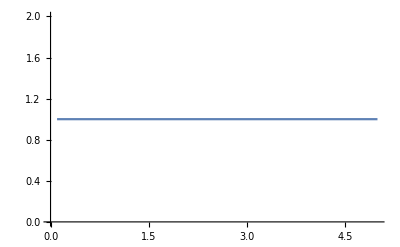

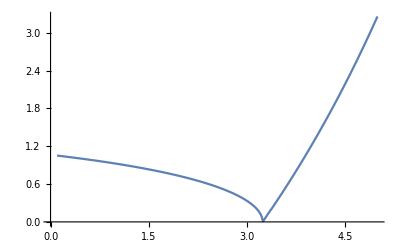

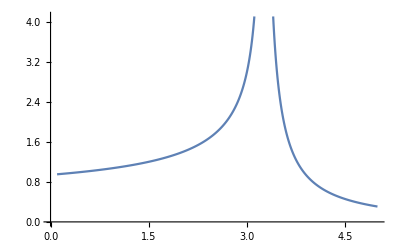

```mathematica
params1={bmax->2.1,μ->1.1,γmax->3,v0->0.1,δ->2,βmax->0.1,h->10,he->1,λmax->20};
fitgradH1=((μ+v[ϵ]+γ[α]) β'[α]-β[α] γ'[α])/.funcset1/.D[funcset1,α];
fitgradP1=(-λ[ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) λ'[ϵ])/.funcset1/.D[funcset1,ϵ];
(* Find the CoESS *)
coESS1=FindRoot[{fitgradH1/.params1,fitgradP1/.params1},{{α,1},{ϵ,10}}]
(* What is the equilibrium at the coESS? *)
resEquil[[2]]/.funcset1/.params1/.coESS1
(* What is the prevalence of infection at the coESS? *)
coESSprev1=resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset1/.params1/.coESS1
(* Is the equilibrium stable? This is important to check because the ESS analyses that we are assuming we are at a stable equilibrium *)
Eigenvalues[D[{ds,di,dz},{{s,i,z}}]/.resEquil[[2]]/.funcset1/.{sm->0,imp->0,zm->0}/.params1/.coESS1]
(* How does overfeeding affect the prevalence of infection (epidemiology) and the ESS virulence (evolution) *)
(* Recorded as the % overfeeding, % change in prevalence, % change in virulence *)
therapy1=Table[{m,
(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset1/.params1/.{α->m coESS1[[1,2]],ϵ->coESS1[[2,2]]})/coESSprev1,((FindRoot[fitgradP1/.params1/.α->m coESS1[[1,2]],{ϵ,1}])[[1,2]])/coESS1[[2,2]],1/coESSprev1(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset1/.params1/.{α->m coESS1[[1,2]],ϵ->(FindRoot[fitgradP1/.params1/.α->m coESS1[[1,2]],{ϵ,1}])[[1,2]]})},{m,0.1,5,0.01}];
ListLinePlot[therapy1[[;;,{1,2}]]] (* change in prevalence *)
ListLinePlot[therapy1[[;;,{1,3}]]] (* change in virulence *)
ListLinePlot[therapy1[[;;,{1,4}]]] (* change in prevalence when exploitation is at ESS *)
```

For the next case, overfeeding will increase birth rate, decrease recovery, and increase shedding. Over epidemiological timescales, this drives an increase in infection prevalence (because there are more hosts around and higher shedding of parasites into the environment). Over evolutionary timescales, this leads to an decrease in virulence. This drives an eco-evolutionary increase in prevalence, even compared to the increase seen in the absence of evolution.

{α→0.511808,ϵ→5.14462}

{s→9.60001,i→6.77016,z→14.8622}

0.413567

{-14.4421+0. ⅈ,-0.109464+0.92928 ⅈ,-0.109464-0.92928 ⅈ}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

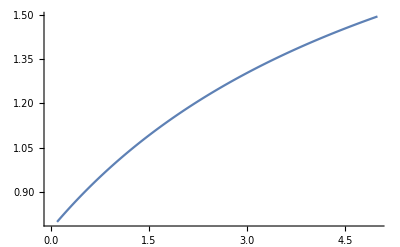

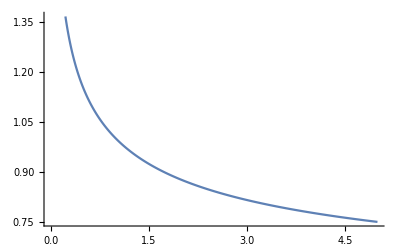

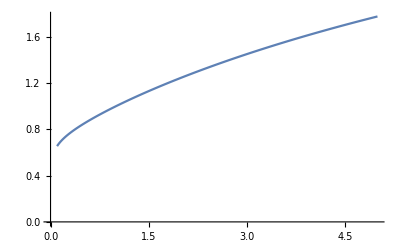

```mathematica
(* Case 2: Anorexia as an Anti-growth resistance mechanism *)
params2={bmax->2.1,μ->1.1,γmax->3,h->1,he->1,βmax->0.3,δ->2,λmax->25,v0->0.2,a->0.5,e->0.1}; 
funcset2={bs[α]->bmax, β[α]->βmax,v[α,ϵ]->v0 ϵ,bi[α]->bmax α/(h+α),γ[α]->γmax/α^a,bi'[α]->D[bmax α/(h+α),α],γ'[α]->D[γmax/α^a,α],λ[α,ϵ]->λmax α ϵ/(he+ϵ),v[ϵ]->v0 ϵ,Derivative[0,1][λ][α,ϵ]->D[λmax α ϵ/(he+ϵ),ϵ],v'[ϵ]->v0};
fitgradH2=Simplify[((μ+v[ϵ]+γ[α]) bi'[α]+(μ-bi[α]+v[ϵ]) γ'[α])/.funcset2];
fitgradP2=(-λ[α,ϵ] v'[ϵ]+(μ+v[ϵ]+γ[α]) Derivative[0,1][λ][α,ϵ])/.funcset2;
(* Find the CoESS *)
coESS2=FindRoot[{fitgradH2/.params2,fitgradP2/.params2},{{α,0.001},{ϵ,1}}]
(* What is the equilibrium at the coESS? *)
resEquil[[2]]/.funcset2/.params2/.coESS2
(* What is the prevalence of infection at the coESS? *)
coESSprev2=resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset2/.params2/.coESS2
(* Is the equilibrium stable? This is important to check because the ESS analyses were assuming we are at a stable equilibrium *)
Eigenvalues[D[{ds,di,dz},{{s,i,z}}]/.resEquil[[2]]/.funcset2/.{sm->0,imp->0,zm->0}/.params2/.coESS2]
(* How does overfeeding affect the prevalence of infection (epidemiology) and the ESS virulence (evolution) *)
(* Recorded as the % overfeeding, % change in prevalence, % change in virulence *)
therapy2=Table[{m,
(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset2/.params2/.{α->m coESS2[[1,2]],ϵ->coESS2[[2,2]]})/coESSprev2,((FindRoot[fitgradP2/.params2/.α->m coESS2[[1,2]],{ϵ,1}])[[1,2]])/coESS2[[2,2]],1/coESSprev2(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset2/.params2/.{α->m coESS2[[1,2]],ϵ->(FindRoot[fitgradP2/.params2/.α->m coESS2[[1,2]],{ϵ,1}])[[1,2]]})},{m,0.1,5,0.01}];
ListLinePlot[therapy2[[;;,{1,2}]]] (* change in prevalence *)
ListLinePlot[therapy2[[;;,{1,3}]]] (* change in virulence *)
ListLinePlot[therapy2[[;;,{1,4}]]] (* change in prevalence when exploitation is at ESS *)
```

For the third case, overfeeding will increase virulence and host birth rate. Over epidemiological timescales, this drives a decrease in infection prevalence (because more hosts are dying of infection). Over evolutionary timescales, this leads to a decrease in virulence (overriding the effects of overfeeding on virulence). However, this decrease in virulence drives an eco-evolutionary increase in prevalence for small amounts of overfeeding, and a decrease for large amounts of overfeeding.

{α→0.641592,ϵ→3.44174}

{s→11.5737,i→8.02065,z→33.9856}

0.409334

{-10.5023+0. ⅈ,-0.128862+1.17654 ⅈ,-0.128862-1.17654 ⅈ}

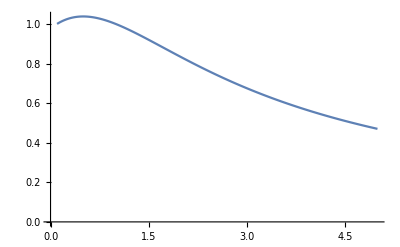

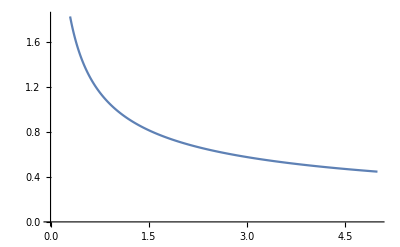

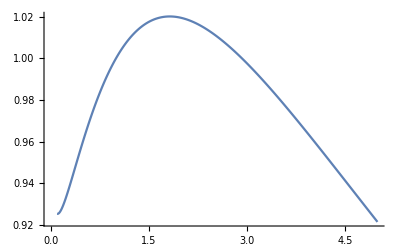

1.02023

```mathematica
(* Context 3: Anorexia as an Anti-growth resistance mechanism but with immunopathology *)
params3={bmax->3,μ->1.8,γmax->2,h->1,he->1,βmax->0.1,δ->2.5,λmax->20,v0->0.5,a->0.2,e->0.05};
funcset3={bs[α]->bmax, β[α]->βmax,γ[α]->γmax,λ[α,ϵ]->(λmax ϵ)/(he+ϵ),v[α,ϵ]->v0 α ϵ, bi[α]->bmax α/(h+α),Derivative[1,0][v][α,ϵ]->v0 ϵ, bi'[α]->D[bmax α/(h+α),α],λ[ϵ]->(λmax ϵ)/(he+ϵ),Derivative[0,1][v][α,ϵ]->v0 α,  λ'[ϵ]->D[(λmax ϵ)/(he+ϵ),ϵ]};
fitgradH3=((γmax+μ+v[α,ϵ]) bi'[α]-(γmax+bi[α]) Derivative[1,0][v][α,ϵ])/.funcset3;
fitgradP3=((γmax+μ+v[α,ϵ]) λ'[ϵ]-λ[ϵ] Derivative[0,1][v][α,ϵ])/.funcset3;
(* Find the CoESS *)
coESS3=FindRoot[{fitgradH3/.params3,fitgradP3/.params3},{{α,0.001},{ϵ,1}}]
(* What is the equilibrium at the coESS? *)
resEquil[[2]]/.funcset3/.params3/.coESS3
(* What is the prevalence of infection at the coESS? *)
coESSprev3=resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset3/.params3/.coESS3
(* Is the equilibrium stable? This is important to check because the ESS analyses were assuming we are at a stable equilibrium *)
Eigenvalues[D[{ds,di,dz},{{s,i,z}}]/.resEquil[[2]]/.funcset3/.{sm->0,imp->0,zm->0}/.params3/.coESS3]
(* How does overfeeding affect the prevalence of infection (epidemiology) and the ESS virulence (evolution) *)
(* Recorded as the % overfeeding, % change in prevalence, % change in virulence *)
therapy3=Table[{m,
(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset3/.params3/.{α->m coESS3[[1,2]],ϵ->coESS3[[2,2]]})/coESSprev3,((FindRoot[fitgradP3/.params3/.α->m coESS3[[1,2]],{ϵ,1}])[[1,2]])/coESS3[[2,2]],1/coESSprev3(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset3/.params3/.{α->m coESS3[[1,2]],ϵ->(FindRoot[fitgradP3/.params3/.α->m coESS3[[1,2]],{ϵ,1}])[[1,2]]})},{m,0.1,5,0.01}];
ListLinePlot[therapy3[[;;,{1,2}]]] (* change in prevalence *)
ListLinePlot[therapy3[[;;,{1,3}]]] (* change in virulence *)
ListLinePlot[therapy3[[;;,{1,4}]]] (* change in virulence *)
Max[therapy3[[;;,4]]]
```

```mathematica
(* Why does increasing feeding decrease ES exploitation, even as it increases virulence? That is counter-intuitive, and thus may be worth emphasizing *)
SingCond=Solve[(((γmax+μ+v[α,ϵ]) λ'[ϵ]-λ[ϵ] Derivative[0,1][v][α,ϵ])/.{ϵ->ϵhat[α]})==0,λ'[ϵhat[α]]]
Solve[Simplify[D[((γmax+μ+v[α,ϵ]) λ'[ϵ]-λ[ϵ] Derivative[0,1][v][α,ϵ])/.{ϵ->ϵhat[α]},α]/.SingCond[[1]]]==0,ϵhat'[α]]//Simplify
```

{{λ'[ϵhat[α]]→(λ[ϵhat[α]] v^(0,1)[α,ϵhat[α]])/(γmax+μ+v[α,ϵhat[α]])}}

{{ϵhat'[α]→(λ[ϵhat[α]] (-v^(0,1)[α,ϵhat[α]] v^(1,0)[α,ϵhat[α]]+(γmax+μ+v[α,ϵhat[α]]) v^(1,1)[α,ϵhat[α]]))/((γmax+μ+v[α,ϵhat[α]]) ((γmax+μ+v[α,ϵhat[α]]) λ''[ϵhat[α]]-λ[ϵhat[α]] v^(0,2)[α,ϵhat[α]]))}}

The denominator of the above expression is negative because it contains the ESS condition (which we know is negative). The first term of the numerator is negative, so if v^(1,1)[α,ϵhat[α]]≤ 0 (e.g., it will be 0 if α and ϵ have additive effects on virulence), then increasing feeding will increase exploitation. But if there is a non-additive effect, then it is possible for increased feeding to drive an increase in virulence, which is counter-intuitive.

For the fourth case, overfeeding will decrease both recovery and virulence. Over epidemiological timescales, this drives an increase in infection prevalence. Over evolutionary timescales, this leads to an increase in virulence (overriding the effects of overfeeding on virulence). The eco-evolutionary effect is to increase prevalence, but less so than the purely ecological case (because of the increase virulence).

{α→0.0610404,ϵ→2.17163}

{s→6.53971,i→4.51984,z→53.6367}

0.408682

{-13.1847+0. ⅈ,-0.0467799+0.540477 ⅈ,-0.0467799-0.540477 ⅈ}

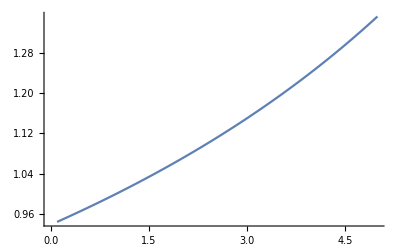

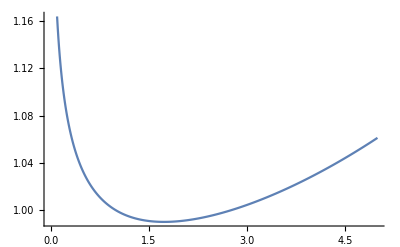

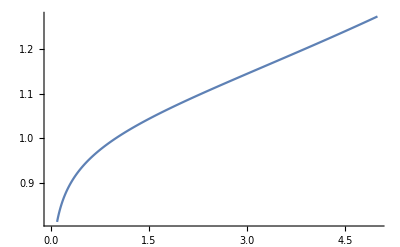

```mathematica
(* Context 4: Anorexia as a Tolerance mechanism *)
(* Parameters for this case *)
params4={bmax->4,μ->3,γmax->1,h->1,he->1,βmax->0.1,δ->0.5,λmax->20,v0->1.2,a->0.3,e->1};
(* Functional forms for this case *)
funcset4={bs[α]->bmax,bi[α]->bmax,β[α]->βmax,λ[α,ϵ]->(ϵ λmax)/(he+ϵ),γ[α]->α^-a γmax,v[α,ϵ]->v0 (1-e α) ϵ,γ'[α]->-a α^(-1-a) γmax,Derivative[1,0][v][α,ϵ]->-e v0 ϵ,λ[ϵ]->(ϵ λmax)/(he+ϵ),λ'[ϵ]->-(ϵ λmax)/(he+ϵ)^2+λmax/(he+ϵ),Derivative[0,1][v][α,ϵ]->v0 (1-e α)};
(* Compute the fitness gradients for host and parasite *)
fitgradH4=((-bmax+μ+v[α,ϵ]) γ'[α]-(bmax+γ[α]) Derivative[1,0][v][α,ϵ])/.funcset4;
fitgradP4=λ'[ϵ]/λ[ϵ]-(Derivative[0,1][v][α,ϵ])/(μ+v[α,ϵ]+γ[α])/.funcset4;
(* Find the CoESS *)
coESS4=FindRoot[{fitgradH4/.params4,fitgradP4/.params4},{{α,0.001},{ϵ,1}}]
(* What is the equilibrium at the coESS? *)
resEquil[[2]]/.funcset4/.params4/.coESS4
(* What is the prevalence of infection at the coESS? *)
coESSprev4=resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset4/.params4/.coESS4
(* Is the equilibrium stable? This is important to check because the ESS analyses were assuming we are at a stable equilibrium *)
Eigenvalues[D[{ds,di,dz},{{s,i,z}}]/.resEquil[[2]]/.funcset4/.{sm->0,imp->0,zm->0}/.params4/.coESS4]
(* How does overfeeding affect the prevalence of infection (epidemiology) and the ESS virulence (evolution) *)
(* Recorded as the % overfeeding, % change in prevalence, % change in virulence *)
therapy4=Table[{m,
1/coESSprev4(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset4/.params4/.{α->m coESS4[[1,2]],ϵ->coESS4[[2,2]]}),((FindRoot[fitgradP4/.params4/.α->m coESS4[[1,2]],{ϵ,1}])[[1,2]])/coESS4[[2,2]],1/coESSprev4(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset4/.params4/.{α->m coESS4[[1,2]],ϵ->(FindRoot[fitgradP4/.params4/.α->m coESS4[[1,2]],{ϵ,1}])[[1,2]]})},{m,0.1,5,0.01}];
ListLinePlot[therapy4[[;;,{1,2}]]] (* change in prevalence *)
ListLinePlot[therapy4[[;;,{1,3}]]] (* change in virulence *)
ListLinePlot[therapy4[[;;,{1,4}]]] (* change in prevalence at new ESS *)
```

```mathematica
(* Again, this result is a bit counterintuitive *)
SingCond=Solve[(λ'[ϵ]/λ[ϵ]-(Derivative[0,1][v][α,ϵ])/(μ+v[α,ϵ]+γ[α])/.{ϵ->ϵhat[α]})==0,λ'[ϵhat[α]]]
Simplify[Solve[(D[λ'[ϵ]/λ[ϵ]-(Derivative[0,1][v][α,ϵ])/(μ+v[α,ϵ]+γ[α])/.{ϵ->ϵhat[α]},α]/.SingCond[[1]])==0,ϵhat'[α]]]
```

{{λ'[ϵhat[α]]→(λ[ϵhat[α]] v^(0,1)[α,ϵhat[α]])/(μ+v[α,ϵhat[α]]+γ[α])}}

{{ϵhat'[α]→(λ[ϵhat[α]] (-γ'[α] v^(0,1)[α,ϵhat[α]]-v^(0,1)[α,ϵhat[α]] v^(1,0)[α,ϵhat[α]]+(μ+v[α,ϵhat[α]]+γ[α]) v^(1,1)[α,ϵhat[α]]))/((μ+v[α,ϵhat[α]]+γ[α]) ((μ+v[α,ϵhat[α]]+γ[α]) λ''[ϵhat[α]]-λ[ϵhat[α]] v^(0,2)[α,ϵhat[α]]))}}

Again, the denominator is negative. The numerator is positive, meaning that overfeeding drives a decrease in exploitation, unless there is a multiplicative effect of α and ϵ on virulence that gives v^(1,1)[α,ϵhat[α]]<0.

```mathematica
Export["therapy1.csv",therapy1]
```

therapy1.csv

```mathematica
Export["therapy2.csv",therapy2]
Export["therapy3.csv",therapy3]
Export["therapy4.csv",therapy4]
```

therapy2.csv

therapy3.csv

therapy4.csv

Also export the original coevolutionary values to create a new version of each figure.

```mathematica
Export["coESSstates.csv",{Append[coESS1[[;;,2]],coESSprev1],
Append[coESS2[[;;,2]],coESSprev2],
Append[coESS3[[;;,2]],coESSprev3],
Append[coESS4[[;;,2]],coESSprev4]}]
```

coESSstates.csv

```mathematica
resEquil
```

{{s→0,i→0,z→0},{s→-(δ (μ+v[α,ϵ]+γ[α]))/(β[α] (μ+v[α,ϵ]+γ[α]-λ[α,ϵ])),i→(δ (μ-bs[α]) (μ+v[α,ϵ]+γ[α]))/((μ-bi[α]+v[α,ϵ]) β[α] (μ+v[α,ϵ]+γ[α]-λ[α,ϵ])),z→-((μ-bs[α]) (μ+v[α,ϵ]+γ[α]))/((μ-bi[α]+v[α,ϵ]) β[α])}}

```mathematica
D[funcset1,α]
```

{bs'[α]→0,bi'[α]→0,β'[α]→2 α βmax,γ'[α]→-(α γmax)/(h+α)^2+γmax/(h+α),0→0,λ^(1,0)[α,ϵ]→0,v^(1,0)[α,ϵ]→0,0→0}

```mathematica
params1
```

{bmax→2.05,μ→1.8,v0→0.1,δ→40,βmax→0.1,h→5,he→1,γmax→2.1,λmax→6}

```mathematica
params2
```

{bmax→2.1,μ→1.1,γmax→3,h→1,he→1,βmax→0.3,δ→2,λmax→25,v0→0.2,a→0.5,e→0.1}

```mathematica
params3
```

{bmax→3,μ→1.8,γmax→2,h→1,he→1,βmax→0.1,δ→2.5,λmax→20,v0→0.5,a→0.2,e→0.05}

```mathematica
params4
```

{bmax→4,μ→3,γmax→1,h→1,he→1,βmax→0.1,δ→0.5,λmax→20,v0→1.2,a→0.3,e→1.}

```mathematica
(* Code for numerical solutions *)
mutfree={sm->0,imp->0,imh->0,zm->0};
tdepvars={s->s[t],i->i[t],z->z[t]};
sol=NDSolve[Join[{s'[t]==(ds/.funcset4/.mutfree/.params4/.coESS4/.tdepvars),
i'[t]==(di/.funcset4/.mutfree/.params4/.coESS4/.tdepvars),
z'[t]==(dz/.funcset4/.mutfree/.params4/.coESS4/.tdepvars),
s[0]==10,i[0]==0,z[0]==1}],
{s,i,z},{t,0,100}];
```

## Context 5: Detailed analysis of model of anorexia as parasite adaptation

For this model, the parasite controls both feeding and exploitation. This is a more challenging case to analyze, in many ways, because we have to assume that there is a cost to the parasite of inducing anorexia, as well as a benefit. For exploitation, we make the conventional assumption that exploitation increases both virulence and shedding. For anorexia to be adaptive for the parasite, it must either increase shedding, decrease recovery, or decrease virulence. The opposite of any of those would be the natural cost of anorexia.

```mathematica
(* parasite traits = α, ϵ *)
(* resident susceptible host *)
ds=bmax s+bmax i-βmax s z-βmax s zm-μ s+γ[α]i+γ[αm] im;
(* resident host infected with resident parasite *)
di=βmax s z-(μ+v[α,ϵ]+γ[α])i;
(* resident host infected with mutant parasite *)
dim=βmax s zm-(μ+v[αm,ϵm]+γ[αm]) im;
(* resident free-living parasite *)
dz=λ[α,ϵ] i-βmax s z-δ z;
(* mutant free-living parasite *)
dzm=λ[αm,ϵm] im-βmax s zm-δ zm;
```

```mathematica
(* parasite invasion fitness using the NGT *)
J=D[{ds,di,dz,dim,dzm},{{s,i,z,im,zm}}];
MatrixForm[J/.{im->0,zm->0}];
F={{0,βmax s},{λ[αm,ϵm],0}};
V={{-(-μ-v[αm,ϵm]-γ[αm]),0},{0,-(-δ-s βmax)}};
(J/.{im->0,zm->0})[[4;;5,4;;5]]==F-V
Inverse[V];
Eigenvalues[-V];
invfitP=((Eigenvalues[F.Inverse[V]])[[2]])^2
```

True

(s βmax λ[αm,ϵm])/((s βmax+δ) (μ+v[αm,ϵm]+γ[αm]))

```mathematica
resEquil=Simplify[Solve[{ds==0,di==0,dz==0}/.{im->0,zm->0},{s,i,z}]]
```

{{s→0,i→0,z→0},{s→-(δ (μ+v[α,ϵ]+γ[α]))/(βmax (μ+v[α,ϵ]+γ[α]-λ[α,ϵ])),i→(δ (bmax-μ) (μ+v[α,ϵ]+γ[α]))/(βmax (bmax-μ-v[α,ϵ]) (μ+v[α,ϵ]+γ[α]-λ[α,ϵ])),z→-((bmax-μ) (μ+v[α,ϵ]+γ[α]))/(βmax (bmax-μ-v[α,ϵ]))}}

We must make an assumption about whether α and ϵ can evolve independently, or whether they are correlated with one another. If they can be related by a function, then there really is only one trait, and the evolutionary analysis is rather simple. If they are free to evolve independently, then what we are looking for is the simultaneous vanishing of the fitness gradients for each trait. Let’s assume the latter for now.

For a singular α to exist, you need some things to hold. In particular, since anorexia benefits the parasite, we have γ’(α) > 0 (decreasing feeding decreases recovery), ∂v/∂α < 0 (decreasing feeding increases virulence) and ∂λ/∂α < 0 (decreasing feeding increases shedding). Thus for there to be a singular α value, it must be the case that |∂v/∂α| > |γ’(α)| (virulence increases faster than recovery decreases); otherwise feeding should just decrease to zero. Any singular α value will be an ESS if, for example γ’’(α)>0, ∂^2 v/∂α^2>0, and ∂^2 λ^2/∂α^2<0. This would mean that recovery is an concave up function of feeding, virulence is a concave down function of feeding, and shedding is a concave down function of feeding. For example, something like v = v_0/α^2 would give derivatives of the correct sign.

```mathematica
(* the fitness gradient in α *)
fitgradα=Numerator[Simplify[D[invfitP,αm]]][[3]]/.{αm->α,ϵm->ϵ}
ESScondα=Numerator[Simplify[D[invfitP,{αm,2}]/.{αm->α,ϵm->ϵ}/.Solve[fitgradα==0,γ'[α]][[1]]]][[3]]
```

-λ[α,ϵ] (γ'[α]+v^(1,0)[α,ϵ])+(μ+v[α,ϵ]+γ[α]) λ^(1,0)[α,ϵ]

-λ[α,ϵ] (γ''[α]+v^(2,0)[α,ϵ])+(μ+v[α,ϵ]+γ[α]) λ^(2,0)[α,ϵ]

For exploitation, the normal rules apply - virulence and shedding are increasing functions of exploitation, but shedding is a saturating function.

```mathematica
(* the fitness gradient in ϵ *)
fitgradϵ=Numerator[Simplify[D[invfitP,ϵm]]][[3]]/.{αm->α,ϵm->ϵ}
ESScondϵ=Numerator[Simplify[D[invfitP,{ϵm,2}]/.{αm->α,ϵm->ϵ}/.Solve[fitgradϵ==0,Derivative[0,1][v][α,ϵ]]][[1]]][[3]]
```

-λ[α,ϵ] v^(0,1)[α,ϵ]+(μ+v[α,ϵ]+γ[α]) λ^(0,1)[α,ϵ]

-λ[α,ϵ] v^(0,2)[α,ϵ]+(μ+v[α,ϵ]+γ[α]) λ^(0,2)[α,ϵ]

What happens if you increase feeding? Can we state with any generality what will happen to ES exploitation? Figure this out using implicit differentiation of the singular strategy condition.

```mathematica
Solve[(fitgradϵ/.{ϵ->ϵhat[α]})==0,Derivative[0,1][λ][α,ϵhat[α]]][[1]]
```

{λ^(0,1)[α,ϵhat[α]]→(λ[α,ϵhat[α]] v^(0,1)[α,ϵhat[α]])/(μ+v[α,ϵhat[α]]+γ[α])}

The change in the ES exploitation with α is given below. Note that the denominator is the ESS condition, implying that the denominator is negative. Thus it will depend entirely on the sign of the numerator. Breaking that down: 
(γ'[α]+v^(1,0)[α,ϵ̂])<0 for a singular strategy to exist at all; 
λ^(0,1)[α,ϵ̂] (γ'[α]+v^(1,0)[α,ϵ̂])<0 since increasing exploitation increases shedding;
-v^(0,1)[α,ϵ̂] λ^(1,0)[α,ϵ̂]>0 since increasing exploitation increases virulence but increasing feeding decreases shedding;
-λ[α,ϵ̂] v^(1,1)[α,ϵ̂] has indeterminate sign, but is likely negative since ∂v/∂α has the opposite sign of ∂v/∂ϵ or is zero if the effects of each are additive;
 (μ+v[α,ϵ̂]+γ[α]) λ^(1,1)[α,ϵ̂]also has indeterminate sign but is likely negative. 
 
 Thus it is very, very likely that the numerator will be negative, implying that the overall derivative will be positive - increased feeding will drive the evolution of increased virulence.

```mathematica
FullSimplify[Solve[D[(fitgradϵ/.{ϵ->ϵhat[α]})==0,α],ϵhat'[α]]]/.ϵhat[α]->ϵ̂
```

{{ϵhat'[α]→(λ^(0,1)[α,ϵ̂] (γ'[α]+v^(1,0)[α,ϵ̂])-v^(0,1)[α,ϵ̂] λ^(1,0)[α,ϵ̂]-λ[α,ϵ̂] v^(1,1)[α,ϵ̂]+(μ+v[α,ϵ̂]+γ[α]) λ^(1,1)[α,ϵ̂])/(λ[α,ϵ̂] v^(0,2)[α,ϵ̂]-(μ+v[α,ϵ̂]+γ[α]) λ^(0,2)[α,ϵ̂])}}

Try out these functional forms:

```mathematica
funcset5={λ[α,ϵ]->(λmax α ϵ)/(he+α ϵ),Derivative[1,0][λ][α,ϵ]->D[(λmax α ϵ)/(he+α ϵ),α],Derivative[2,0][λ][α,ϵ]->D[(λmax α ϵ)/(he+α ϵ),{α,2}],Derivative[0,1][λ][α,ϵ]->D[(λmax α ϵ)/(he+α ϵ),ϵ],Derivative[0,2][λ][α,ϵ]->D[(λmax α ϵ)/(he+α ϵ),{ϵ,2}],
γ[α]->γmax α,γ'[α]->D[γmax α,α],v[α,ϵ]->(v0 ϵ)/α,Derivative[1,0][v][α,ϵ]->D[(v0 ϵ)/α,α],Derivative[2,0][v][α,ϵ]->D[(v0 ϵ)/α,{ϵ,2}],Derivative[0,1][v][α,ϵ]->D[(v0 ϵ)/α,ϵ],Derivative[0,2][v][α,ϵ]->D[(v0 ϵ)/α,{ϵ,2}]};
```

```mathematica
params5={bmax->3,μ->2.8,γmax->1,h->1,he->1,βmax->0.1,δ->1,λmax->15,v0->1,a->0.3,e->1.};
ESSϵ=Solve[(fitgradϵ/.funcset5)==0,ϵ]/.params5;
ESSα=FindRoot[(fitgradα/.funcset5/.ESSϵ[[2]]/.params5),{α,1}];
ESSϵ=ESSϵ[[2]]/.ESSα;
coESS5=Join[ESSα,ESSϵ]
resEquil[[2]]/.funcset5/.params5/.coESS5
coESSprev=resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset5/.params5/.coESS5
Eigenvalues[D[{ds,di,dz},{{s,i,z}}]/.resEquil[[2]]/.funcset5/.{sm->0,im->0,zm->0}/.params5/.coESS5]
therapy5=Table[{m,
(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset5/.params5/.{α->m coESS5[[1,2]],ϵ->coESS5[[2,2]]})/coESSprev,((Solve[(fitgradϵ/.funcset5)==0,ϵ]/.params5/.α->m coESS5[[1,2]])[[2,1,2]])/coESS5[[2,2]],(resEquil[[2,2,2]]/(resEquil[[2,1,2]]+resEquil[[2,2,2]])/.funcset5/.params5/.{α->m coESS5[[1,2]],ϵ->(Solve[(fitgradϵ/.funcset5)==0,ϵ]/.params5/.α->m coESS5[[1,2]])[[2,1,2]]})/coESSprev},{m,1,5,0.01}];
```

{α→2.10458,ϵ→2.21463}

{s→9.31728,i→2.18641,z→13.9785}

0.190062

{-8.98866+0. ⅈ,-0.0488929+0.360765 ⅈ,-0.0488929-0.360765 ⅈ}

```mathematica
Export["~/Box Sync/Research/Jessica_Hite/AnorexiaReview/therapy5.csv",therapy5]
```

~/Box Sync/Research/Jessica_Hite/AnorexiaReview/therapy5.csv